# Young Diagrams and Tableaux

## Willoughby Seago MPhys Project

Here’s some setup, just ignore it.

```mathematica
On[Assert]
```

```mathematica
debug::msg="Debug: `1`";
```

```mathematica
debug[msg_]:=Message[debug::msg,msg]
```

```mathematica
debug["TEST"]
```

debug::msg: Debug: TEST

```mathematica
On[debug::msg]
```

## Young Diagrams

Let  be a positive integer. A partition, , of  is a list of values,  such that . For example, suppose , then one partition is , another is , and a third is .
We will only be interested in ordered partitions, where . In this case we can represent each such partition with  boxes arranged into  columns (which may not all be filled) and  rows. The first row will contain  boxes, the second  boxes, and so on, up to the final row with  boxes. This is called the Young diagram for the partition.
For example, the partition  is represented by

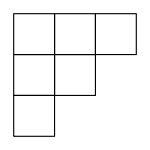

```mathematica
Graphics[{EdgeForm[Thick],FaceForm[None],Rectangle/@{{0,0},{1,0},{2,0},{0,-1},{1,-1}},Rectangle[{0,-2}]},ImageSize->{150,150}]
```

the partition  is represented by

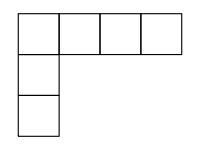

```mathematica
Graphics[{EdgeForm[Thick],FaceForm[None],Rectangle/@{{0,0},{1,0},{2,0},{3,0},{0,-1},{0,-2}}},ImageSize->{200,150}]
```

and the partition  is represented by

```mathematica
Graphics[{EdgeForm[Thick],FaceForm[None],Rectangle/@{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0}}},ImageSize->{300,50}]
```

-Graphics-

We can write a function which draws a Young diagram for an arbitrary partition:

We start with a helper function to test if a list is sorted in decreasing order

```mathematica
isSortedDescending[{x_}]:=True  (* base case, a one element list is sorted *)
```

```mathematica
isSortedDescending[list_List]:=list[[1]]>=list[[2]]&&isSortedDescending[Rest[list]]  (* a list is sorted if the first element is bigger than the second and the rest is sorted *)
```

Now we implement the Young diagram:

```mathematica
Options[printYoungDiagram]:={"boxSize"->50}
```

```mathematica
printYoungDiagram[partition:{__Integer}/;AllTrue[partition,Positive],OptionsPattern[]]:=
Module[
{boxCorners,boxSize=OptionValue["boxSize"],imageWidth,imageHeight},
Assert[isSortedDescending[partition]];  (* Young diagrams can only be formed from ordered partitions *)
boxCorners=Table[{i,-j},{j,1,Length[partition]},{i,0,(partition[[j]])-1}];  (* positions of bottom left corners of boxes *)
(* Compute size of final Graphics object, boxSize is measured in printers points (1/72 of an inch) *)
imageWidth=partition[[1]]*boxSize;
imageHeight=Length[partition]*boxSize;
(* Create Young diagram Graphics object *)
Graphics[{EdgeForm[Thick],FaceForm[None],Rectangle/@Flatten[boxCorners,1]},ImageSize->{imageWidth,imageHeight}]
];
```

```mathematica
printYoungDiagram[{3,2,1}]
```

-Graphics-

```mathematica
printYoungDiagram[{4,1,1}]
```

-Graphics-

```mathematica
printYoungDiagram[{6}]
```

-Graphics-

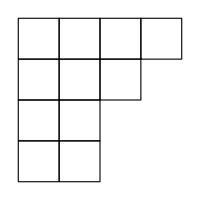

```mathematica
printYoungDiagram[{4,3,2,2}]
```

## Young Tableaux

A Young tableau (pl. Young tableaux) is a Young diagram with numbers in the boxes. It’s that simple.

```mathematica
Options[printYoungTableau]:={"boxSize"->50,"FontSize"->25,"ColorFunction"->Identity}
```

```mathematica
printYoungTableau[youngTableau[numbers_List],OptionsPattern[]]:=
Module[
{partition=Length/@numbers,boxCorners,boxSize=OptionValue["boxSize"],imageWidth,imageHeight,numberPositions},
Assert[isSortedDescending[partition]];  (* Young diagrams can only be formed from ordered partitions *)
boxCorners=Table[{i,-j},{j,1,Length[partition]},{i,0,(partition[[j]])-1}];  (* positions of bottom left corners of boxes *)
(* Compute size of final Graphics object, boxSize is measured in printers points (1/72 of an inch) *)
imageWidth=partition[[1]]*boxSize;
imageHeight=Length[partition]*boxSize;
(* Compute number positions *)
numberPositions=Transpose@{Flatten[numbers],Flatten[Table[{(i+1/2),(-j+1/2)},{j,1,Length[partition]},{i,0,(partition[[j]])-1}],1]};
(* Create Young diagram Graphics object *)
Graphics[{
EdgeForm[Thick],
FaceForm[None],
Rectangle/@Flatten[boxCorners,1],
FontSize->OptionValue["FontSize"],
OptionValue["ColorFunction"]@(Text@@@numberPositions)
},
ImageSize->{imageWidth,imageHeight}]
];
```

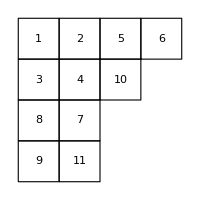

```mathematica
printYoungTableau[youngTableau[{{1,2,5,6},{3,4,10},{8,7},{9,11}}]]
```

A standard tableau is a Young tableau in which the numbers are such that they increase to the right and downwards. For example, the list of all three box standard tableaux is

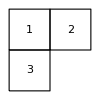
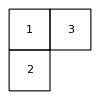
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{
printYoungTableau[youngTableau[{{1,2},{3}}]],
printYoungTableau[youngTableau[{{1,3},{2}}]],
printYoungTableau[youngTableau[{{1},{2},{3}}]],
printYoungTableau[youngTableau[{{1,2,3}}]]
}, Spacer[36]]
```

## Internal Representation

In order to represent a Young tableau internally and do maths on it we use a ragged array, which flattens to give the “numbers” argument to printYoungTableau, so the tableau

```mathematica
printYoungTableau[youngTableau[{{1,2,5,6},{3,4,10},{8,7},{9,11}}],boxSize->20, FontSize->10]
```

-Graphics-

is represented by the array

```mathematica
exampleTableau=youngTableau[{{1,2,5,6},{3,8,10},{4,7},{9,11}}];
```

we use the youngTableau wrapper in order to allow for pretty printing of the tableau

```mathematica
Format[youngTableau[numbers_],StandardForm]:=printYoungTableau[youngTableau[numbers]];
Format[youngTableau[numbers_,boxSize->n_],StandardForm]:=printYoungTableau[youngTableau[numbers],boxSize->n];
Format[youngTableau[numbers_,FontSize->f_],StandardForm]:=printYoungTableau[youngTableau[numbers],FontSize->f];
Format[youngTableau[numbers_,FontSize->f_,boxSize->n_],StandardForm]:=printYoungTableau[youngTableau[numbers],boxSize->n,FontSize->f];
Format[youngTableau[numbers_,boxSize->n_,FontSize->f_],StandardForm]:=printYoungTableau[youngTableau[numbers],boxSize->n,FontSize->f];
```

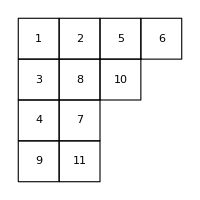

```mathematica
exampleTableau
```

You can still see this array representation with InputForm:

```mathematica
InputForm[exampleTableau]
```

youngTableau[{{1, 2, 5, 6}, {3, 8, 10}, {4, 7}, {9, 11}}]

It is (hopefully) much easier to do maths on this internal representation of a Young Tableau. One simple example is that often we want to sort all of the rows of a tableau so that the numbers in rows appear in increasing order, this can be done using the following method:

```mathematica
sortRows[youngTableau[numbers_]]:=youngTableau[Sort/@numbers]
```

```mathematica
shuffleTableau[youngTableau[numbers_]]:=youngTableau[RandomSample/@numbers]
```

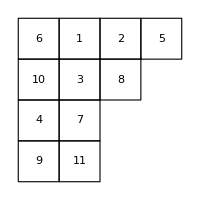
Shuffled | Sorted
-Graphics- | -Graphics-

```mathematica
Block[{shuffledTableau=shuffleTableau[exampleTableau]},Grid[{{"Shuffled","Sorted"},{shuffledTableau,sortRows[shuffledTableau]}}]]
```

## Garnir Relations

A standard tableau is an  box tableau which contains the numbers  to  such that in any row or column they are sorted in increasing order from left to right or top to bottom. For example, the following is a standard tableau

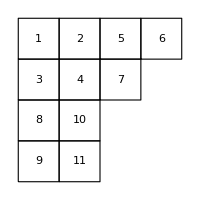

```mathematica
youngTableau[{{1,2,5,6},{3,4,7},{8,10},{9,11}}]
```

but the following is not a standard tableau since 8 appears above 7:

```mathematica
exampleTableau
```

-Graphics-

The following method checks that the numbers  through  are used in an  box tableau, this is the first step to checking if it is a standard tableau

```mathematica
usesAllNumbers[youngTableau[numbers_]]:=Sort[Flatten[numbers]]==Table[i,{i,Total[Length/@numbers]}]
```

```mathematica
usesAllNumbers[exampleTableau]  (* Should be True *)
```

True

```mathematica
usesAllNumbers[youngTableau[{{1,2,3},{5,6}}]]  (* Should be False *)
```

False

The Garnir relations allow us to write any tableau as a sum of standard tableaux. Of course, first we have to define a sum of tableaux. The sum of two  box tableaux is the sum of the projection operators which they label. The first step is to sort the rows of the tableau. This is allowed because the projection operators symmetrise across the rows of the tableau, so we can freely reorder the rows without changing the projection operator.

Next, we have to identify the first problem point, the first point, reading left to right, top to bottom, where a number appears and the number below is larger.
We start with a helper function to compare two lists of different lengths element wise, returning a list of booleans. This list will be the same length as the second list, which is assumed to be the shorter of the two lists (if they have different lengths). Each boolean entry will be True if the first list contains the smaller entry and False otherwise.

```mathematica
compareRaggedLists[list1_List,list2_List]:=Block[{},
Assert[Length[list1]>=Length[list2]];
MapThread[#1<#2&,{list1[[1;;Length[list2]]],list2}]
]
```

```mathematica
compareRaggedLists[{1,2,5,6},{3,8,10}] (* Should be {True, True, True} *)
```

{True,True,True}

```mathematica
compareRaggedLists[{3,8,10},{4,7}] (* Should be {True, False} *)
```

{True,False}

We can now make a function which finds the position, in box numbers, of the first misordered entry, giving the result as a pair of the positions of the box and the box below it.

```mathematica
findMisordering[youngTableau[numbers_]]:=Module[{tableau=sortRows[youngTableau[numbers]],(* sort rows of array *)
rowIndex,comparison,position={}}, 
For[rowIndex=1,rowIndex<=Length[numbers]-1,rowIndex++,  (* for each row in the tableau *)
comparison=compareRaggedLists[numbers[[rowIndex]],numbers[[rowIndex+1]]];(* Compare rows elementwise *)
position=Position[comparison,False,1];  (* Get the position of the first occurence of False in the array *)
If[position!={},Break[]]]; (* If False was found then exit the loop *)
If[position=={},Return[{-1,-1}]];  (* In standard form, use {-1, -1} as a result that cannot be achieved if not sorted *)
Return[{position[[1,1]]+Length[Flatten[numbers[[1;;rowIndex-1]]]],
position[[1,1]]+Length[Flatten[numbers[[1;;rowIndex]]]]}]  (* Not in standard form, return box number of first unsorted box *)
]
```

```mathematica
findMisordering[exampleTableau]
```

{6,9}

```mathematica
findMisordering[youngTableau[{{1,2,5,6},{3,4,7},{8,10},{9,11}}]]
```

{-1,-1}

This function also gives us a way to test if a tableau is in standard form:

```mathematica
isStandardTableau[youngTableau[numbers_]]:=findMisordering[youngTableau[numbers]]=={-1,-1}
```

```mathematica
Assert[Not@isStandardTableau[exampleTableau]]  (* Should give False *)
```

```mathematica
Assert[isStandardTableau[youngTableau[{{1,2,5,6},{3,4,7},{8,10},{9,11}}]] ]  (* Should give True *)
```

Once we know the positions we then operate on all positions between these. It can be useful to visualise this strip of boxes, which we can do as follows:

```mathematica
printColorStrip[youngTableau[numbers_],{a_Integer,b_Integer}]:=
printYoungTableau[youngTableau[numbers],
ColorFunction->(Insert[Insert[#1,Red,a],Black,b+2]&)  (* +2 beacuse we want to insert after this element (+1) and we've inserted an extra Red (+1) *)
]
```

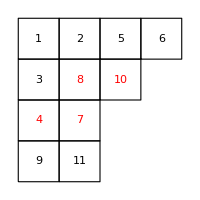

```mathematica
printColorStrip[exampleTableau,findMisordering[exampleTableau]]
```

Once we’ve identified the problem strip we want to generate all permutations which involve at least one swap between the two rows, swaps within a row just correspond to the same diagram since we can always sort the row.
For our example we want the permutations
(6 8), (6 9), (7 8), (7 9), and (6 8)(7 9)
Note that these are in terms of the box number.
Start by finding the misordered part of the list

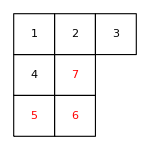

```mathematica
printColorStrip[#,findMisordering[#]]&@youngTableau[{{1,2,3},{4,7},{5,6}}]
```

We now define a pair format for ordered pairs, which we’ll use as part of our data structure, and we want pair[a, b] to pretty print as . Note that these pairs are mostly for internal use, and don’t appear in the final output, so this formatting is just to make debugging easier.

```mathematica
Format[pair[a_,b_],StandardForm]:=⟨a,b⟩
```

We now define a function which takes in a list of numbers, and a point to split them, , and then produces all lists given by permuting the elements between the two lists, up to the order of the lists.
We’ll do this recursively. As well as taking in the list of numbers and the point to split we also take the previous results of the function, which we call left and right, as they contain numbers to the left and right of the split point.
The first base case is when , in this case we simply return a pair of the left numbers, and the right numbers with the unsorted numbers added on to the end.

```mathematica
generatePermutedLists[list_List,0,left_,right_]:=pair[left,Join[right,list]]
```

The next case is when  is equal to the length of the list, so we split at the end of the list, we then simply return a pair of the left numbers with the unsorted numbers appended and then the right numbers.

```mathematica
generatePermutedLists[list_List,k_Integer,left_,right_]:=pair[Join[left,list],right]/;k==Length[list]
```

Next comes the recursive step. We set the head to the first time of the unsorted list, and the tail to the rest. We then recursively call the function twice on the tail, splitting at  and  depending on which list we put the head into.

```mathematica
generatePermutedLists[list_List,k_Integer,left_,right_]:=Module[{head,tail},
head=First[list];
tail=Rest[list];
{generatePermutedLists[tail,k-1,Append[left,head],right],generatePermutedLists[tail,k,left,Append[right,head]]}
]/;k<=Length[list]
```

Next we define a helper function which will take in one of the pairs produced by this function and then generate the permutation we need to apply to the Young Tableau. This permutation is represented as a list of lists, with each sublist containing two elements, {a, b}, meaning “take the thing in spot a and replace it with the thing in spot b” we’ll call this a swap.

```mathematica
pairToSwaps[pairs_]:=Module[{maxNumber,flattenedListPair,permutedList},
flattenedListPair=Flatten[pairs/.pair->List];  (* flatten input and convert pairs to lists *)
maxNumber=Max[flattenedListPair];  (* need to generate a list of at least as many numbers as the maximum box number *)
permutedList=Join[Range[1,Min[flattenedListPair]-1],flattenedListPair];
DeleteCases[Transpose[{Range[maxNumber],permutedList}],{a_,a_}]  (* create pairs from lists and remove elements that don't change *)
]
```

```mathematica
pairToSwaps[{pair[{6,8},{7,9}]}]
```

{{7,8},{8,7}}

We now make another helper function which takes in two lists, which will be the two two strips from the misordered point to the end of the row, and then from the start of the next row to the square below the misordered point, and generates all swaps by calling generatePermutedLists and then converting the output to swaps:

```mathematica
generateSwaps[firstRow_List,secondRow_List]:=pairToSwaps/@Flatten[generatePermutedLists[Join[firstRow,secondRow],Length[firstRow],{},{}]]
```

We now write another helper function to allow us to reshape a ragged array based on another ragged array as a template. This code is taken from https://mathematica.stackexchange.com/a/138034:

```mathematica
reshapeRaggedArray[list_List,template_]:=Module[{i=1},Map[list[[i++]]&,template,{-1}]]
```

```mathematica
reshapeRaggedArray[Range[11],{{1,2,3,4},{5,6,7},{8,9},{10,11}}]
```

{{1,2,3,4},{5,6,7},{8,9},{10,11}}

Now we write a function which takes in a Young Tableau and a list of swaps and applies the swaps to the Young tableau:

```mathematica
applySwaps[youngTableau[numbers_],swaps_List]:=Module[{unpermutedList=Flatten[numbers],permutedList,i},
permutedList=unpermutedList;
(* Iterate through flattened lists making necessary swaps *)
For[i=1,i<=Length[swaps],i++,
permutedList[[swaps[[i,1]]]]=unpermutedList[[swaps[[i,2]]]]
];
(* reshape array and output Young tableau *)
youngTableau[reshapeRaggedArray[permutedList,numbers]]
]
```

```mathematica
applySwaps[exampleTableau,{{6,8},{7,9},{8,6},{9,7}}]
```

-Graphics-

We now write a function which takes a Young tableau and applies the Garnir relation to it once.

```mathematica
applyGarnir[youngTableau[numbers_]]:=Module[{misordering=findMisordering[youngTableau[numbers]],position,canonicalTableau=reshapeRaggedArray[Range[Length[Flatten[numbers]]],numbers],rowLength,row1,row2,swaps},
If[isStandardTableau[sortRows[youngTableau[numbers]]],Return[sortRows[youngTableau[numbers]]]];
position=Position[reshapeRaggedArray[Range[Max[Flatten[numbers]]],numbers],misordering[[1]]];  (* position in ragged array of the misordering *)
rowLength=Length[canonicalTableau[[position[[1,1]]]]]-position[[1,2]]+1 ;(* number of boxes in row after (and including) misordered box *)
row1=Range[misordering[[1]],misordering[[1]]+rowLength-1];
row2=Range[misordering[[1]]+rowLength,misordering[[2]]];
swaps=Rest@generateSwaps[row1,row2];  (* Throw away first result, its the identity and we don't want it *)
applySwaps[youngTableau[numbers],#]&/@swaps
]
```

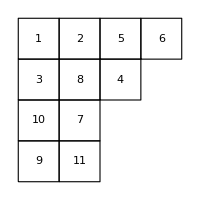
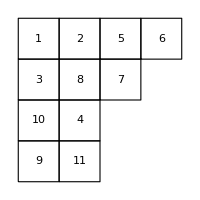
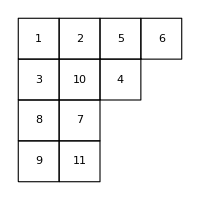
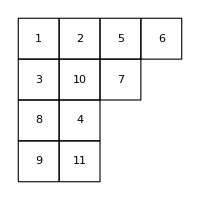
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
applyGarnir[exampleTableau]
```

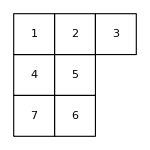
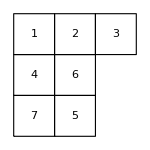

```mathematica
applyGarnir[youngTableau[{{1,2,3},{4,7},{5,6}}]]
```

The next function simply takes this and applies it iteratively until all tableau are standard.

```mathematica
decomposeTableau[youngTableau[numbers_]]:=Module[{tableau=sortRows[youngTableau[numbers]],tableauList},
If[Not@isStandardTableau[tableau],tableauList=applyGarnir[tableau],Return[tableau]];
-Plus@@decomposeTableau/@tableauList
]
```

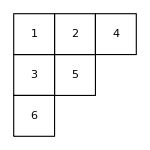
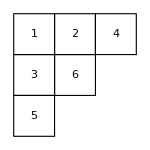
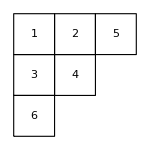
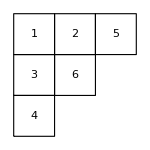
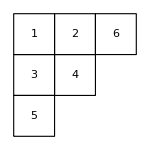
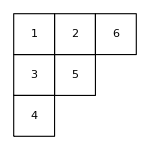
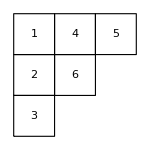
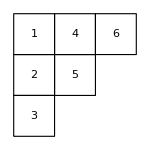
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics---Graphics---Graphics-

```mathematica
decomposeTableau[youngTableau[{{1,6,5},{2,4},{3}}]]
```

## Dimension

Given a young diagram, , with  boxes the dimension of the irrep of  corresponding to this diagram is the number of standard Young tableau with the same shape.
This is given by the formula

where  is the hook number of the diagram, defined as the product of the hook lengths of the diagram, where the hook length of a box in a diagram is the number of boxes to the right and below, plus the box itself. For example, the following diagram has numbers inserted corresponding to the hook length:

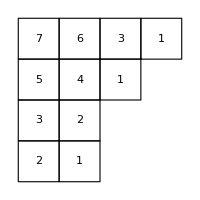

```mathematica
hookLengths[exampleTableau]
```

and the hook number is

```mathematica
hookNumber[exampleTableau]
```

30240

these were computed with the following functions

```mathematica
hookLengths[youngTableau[numbers_]]:=Module[{hookNumbers=numbers,i},
(*Iterate over tableau and compute hook length at each step*)
For[i=1,i<=Length[numbers],++i,
For[j=1,j<=Length[numbers[[i]]],++j,
hookNumbers[[i,j]]=Length[numbers[[i]]]-j+Count[numbers[[i;;]],x_/;Length[x]>=j] 
(* length - j gives number of boxes left in row, count[...] gives number of rows from current row down with boxes left in the current column *)
]];
youngTableau[hookNumbers]]
```

```mathematica
hookNumber[youngTableau[numbers_]]:=Times@@Flatten@@hookLengths@youngTableau[numbers]
```

so we can implement the hook formula as

```mathematica
hookFormula[youngTableau[numbers_]]:=(Length[Flatten[numbers]]!)/hookNumber[youngTableau[numbers]]
```

```mathematica
hookFormula[exampleTableau]
```

1320

The following function generates all standard tableaux of the same shape of the input tableau:

```mathematica
generateStandardTableaux[youngTableau[numbers_]]:=Module[{standardTableaux={},numberOfBoxes,permutations,i,yt,numberOfStandardTableau},
numberOfBoxes=Length[Flatten[numbers]];
permutations=Permutations[Range[numberOfBoxes]];
numberOfStandardTableau=hookFormula[youngTableau[numbers]];
For[i=1,i<=numberOfBoxes!,i++,
yt=sortRows@youngTableau[reshapeRaggedArray[permutations[[i]],numbers]];
If[Not@MemberQ[standardTableaux,yt]&&isStandardTableau[yt],AppendTo[standardTableaux,yt]];
If[Length[standardTableaux]==numberOfStandardTableau,Break[]];
];
standardTableaux
]
```

for example, there are three standard tableaux matching the partition (3, 1):

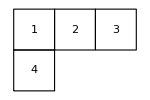
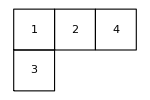
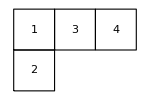

```mathematica
generateStandardTableaux[youngTableau[{{1,2,3},{4}}]]
```

These tableaux will always be generated in the same order, so we can use this order to define an order for the basis of standard tableau. It’s then just a case of taking a tableau decomposed as a sum of standard tableau and generating the matrix that gives this tableau in this basis.

Next we define a “dot product” between standard tableaux which we take to form an orthonormal basis of the group algebra ℂ

```mathematica
standardTableauDotProduct[factor1_. youngTableau[numbers1_]/;NumericQ[factor1],factor2_. youngTableau[numbers2_]/;NumericQ[factor2]]:=Block[{sortedNumbers1=List@@sortRows[youngTableau[numbers1]][[1]],sortedNumbers2=List@@sortRows[youngTableau[numbers2]][[1]]},Assert[And@@isStandardTableau/@youngTableau/@{numbers1,numbers2}];If[sortedNumbers1==sortedNumbers2,factor1*factor2,0]]
```

The following function takes a tableau and returns the permutation generating it by acting on a completely ordered tableau of the same shape

```mathematica
tableauToPermutation[youngTableau[numbers_]]:=Module[{numberOfBoxes=Length[Flatten[numbers]]},FindPermutation[Range[numberOfBoxes],Flatten[numbers]]]
```

The following function takes a tableau and permutation and applies the permutation to the tableau

```mathematica
applyPermutationToTableau[permutation_Cycles,youngTableau[numbers_]]:=Module[{numberOfBoxes=Length[Flatten[numbers]],newTableau},
newTableau=Range[numberOfBoxes];
newTableau=Permute[newTableau,permutation];
newTableau=reshapeRaggedArray[newTableau,numbers];
youngTableau[newTableau]
]
```

We can now calculate the representation of a given permutation, represented with Mathematica’s built in Cycles type, in a given representation labelled by a Young tableau of a given shape

```mathematica
representation[permutation_Cycles,youngTableau[numbers_]]:=Module[{
standardTableaux=generateStandardTableaux[youngTableau[numbers]],
numberOfBoxes=Length[Flatten[numbers]],
permutedTableaux,
tableauxPermutations,
orderedTableau
},
orderedTableau=youngTableau[reshapeRaggedArray[Range[numberOfBoxes],numbers]];  (* tableau filled with numbers 1, 2, 3, ... in order *)
tableauxPermutations=tableauToPermutation/@standardTableaux;  (* turn standard tableaux into permutations acting on the ordered tableaux *)
tableauxPermutations=PermutationProduct[permutation,#]&/@tableauxPermutations;  (* compute product of permutations *)
(* apply product permutation to ordered tableaux *)
permutedTableaux=applyPermutationToTableau[#,orderedTableau]&/@tableauxPermutations;
permutedTableaux=decomposeTableau/@permutedTableaux;  (* decompose result into standard tableaux using Garnir *)
(* compute representation matrix *)
Table[Distribute[standardTableauDotProduct[standardTableaux[[i]],#]]&/@permutedTableaux,{i,1,Length[standardTableaux]}]
]
```

If  is a representation of the symmetric group then for  we should have , since a representation is by definition a homomorphism.
We can use this, in the form , with subtraction just the usual subtraction of matrices, to check that the representations we are computing have the correct relationships. We do so here by constructing the multiplication tables for some of the smaller symmetric groups

```mathematica
testRepresentation[n_Integer/;n>=1,youngTableau[numbers_]]:=Module[{yt=youngTableau[numbers],permutations=GroupElements[SymmetricGroup[n]],multiplicationTable,success},
multiplicationTable=Table[
representation[permutations[[i]],yt].representation[permutations[[j]],yt]-representation[PermutationProduct[permutations[[i]],permutations[[j]]],yt]
,{i,1,n!},{j,1,n!}];
success=AllTrue[#==0&]@Flatten[multiplicationTable];
Assert[success];
If[success,Print["Success: ","n = "<>ToString[n]<>" ",yt],Print["Failure",multiplicationTable]];
]
```

Success: n = 3 -Graphics-

Success: n = 3 -Graphics-

Success: n = 3 -Graphics-

Success: n = 4 -Graphics-

Success: n = 4 -Graphics-

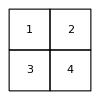
Success: n = 4 -Graphics-

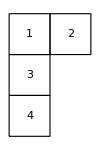
Success: n = 4 -Graphics-

Success: n = 4 -Graphics-

Success: n = 5 -Graphics-

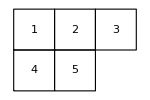
Success: n = 5 -Graphics-

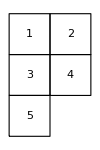
Success: n = 5 -Graphics-

Success: n = 5 -Graphics-

```mathematica
testRepresentation[#[[1]],youngTableau[#[[2]]]]&/@{
{3,{{1,2,3}}},{3,{{1,2},{3}}},{3,{{1},{2},{3}}},  (* All  reps *)
{4,{{1,2,3,4}}},{4,{{1,2,3},{4}}},{4,{{1,2},{3,4}}},{4,{{1,2},{3},{4}}},{4,{{1},{2},{3},{4}}}, (* All  reps *)
{5,{{1,2,3,4,5}}},{5,{{1,2,3},{4,5}}},{5,{{1,2},{3,4},{5}}},{5,{{1},{2},{3},{4},{5}}}  (* Some  reps *)
};
```

For larger groups ( and above) constructing the entire table takes too long, instead the following modification of the above samples the group randomly

```mathematica
testRepresentationSample[n_Integer/;n>=1,youngTableau[numbers_],samples_Integer]:=Module[{yt=youngTableau[numbers],permutations=GroupElements[SymmetricGroup[n]],multiplicationTable,i,j,success},
If[samples>=n!,Return[testRepresentation[n,yt]]];
multiplicationTable=Table[{i,j}={RandomInteger[{1,n!}],RandomInteger[{1,n!}]};
representation[permutations[[i]],yt].representation[permutations[[j]],yt]-representation[PermutationProduct[permutations[[i]],permutations[[j]]],yt]
,{k,1,samples}];
success=AllTrue[#==0&]@Flatten[multiplicationTable];
Assert[success];
If[success,Print["Success: ","n = "<>ToString[n]<>" ",yt],Print["Failure",multiplicationTable]];
]
```

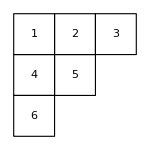
Success: n = 6 -Graphics-

```mathematica
testRepresentationSample[6,youngTableau[{{1,2,3},{4,5},{6}}],100]  (* Test a single  rep, takes about 30 second to run *)
```

## Symmetriseres and Antisymmetrisers

Symmetrisers and antisymmetrisers have almost identical structure, differing only by a sign. This structure is abstracted in to the symmetriser abstract base class, or ABCsymmetriser

```mathematica
ABCsymmetriser[{x_},youngTableau[numbers_],symmetryFactor_]:=representation[Cycles[{{}}],youngTableau[numbers]]
```

```mathematica
ABCsymmetriser[legs_List/;Length[legs]>=2,youngTableau[numbers_],symmetryFactor_]:=Module[{numberOfLegs=Length[legs],identityOnFirstLegSymmetriseEverythingElse=ABCsymmetriser[Rest[legs],youngTableau[numbers],symmetryFactor]},1/numberOfLegs(identityOnFirstLegSymmetriseEverythingElse+symmetryFactor(numberOfLegs-1)identityOnFirstLegSymmetriseEverythingElse.representation[Cycles[{{legs[[1]],legs[[2]]}}],youngTableau[numbers]].identityOnFirstLegSymmetriseEverythingElse)]
```

```mathematica
symmetriser[legs_List,youngTableau[numbers_]]:=ABCsymmetriser[legs,youngTableau[numbers],1]
```

```mathematica
antisymmetriser[legs_List,youngTableau[numbers_]]:=ABCsymmetriser[legs,youngTableau[numbers],-1]
```

Symmetriseres and antisymmeterisers are idempotent, that is , we can test idempotency with the following function

```mathematica
testIdempotency[x_]:=x.x==x
```

## Young Projectors

Young projectors are defined by Young tableaux, numbered 1 to  left to right, top to bottom. We symmetrise over rows and antisymmetrise over columns. The representation of a Young projector can be generated using the following functions

```mathematica
getTableauRows[youngTableau[numbers_]]:=numbers  (* returns list of rows (which are lists of numbers) *)
```

```mathematica
getTableauColumns[youngTableau[numbers_]]:=Flatten[numbers,{2}]  (* returns list of columns (which are lists of numbers) *)
```

```mathematica
youngProjector[youngTableau[projectorNumbers_],youngTableau[representationNumbers_]]:=Module[{rows=getTableauRows[youngTableau[projectorNumbers]],columns=getTableauColumns[youngTableau[projectorNumbers]],symmetrisers,antisymmetrisers,normalisation},
symmetrisers=symmetriser[#,youngTableau[representationNumbers]]&/@rows;
symmetrisers=Dot@@symmetrisers;
antisymmetrisers=antisymmetriser[#,youngTableau[representationNumbers]]&/@columns;
antisymmetrisers=Dot@@antisymmetrisers;
normalisation=1/hookNumber[youngTableau[projectorNumbers]] Times@@(Factorial/@Length/@rows)*Times@@(Factorial/@Length/@columns);
normalisation*symmetrisers.antisymmetrisers
]
```

note that youngProjector takes two Young tableaux as arguments. The first labels the Young projector, the second labels the representation.